```mathematica
Test1[n_]:=Range[Ceiling[(n+1)/2],n]
Test1[4]
Test1[5]
Test1[6]
```

{3,4}

{3,4,5}

{4,5,6}

```mathematica
Condorcet[n_,p_]:=(
res=0;
Do[
(*Print[m];
Print[Binomial[n,m]p^(m)(1-p)^(n-m)];*)
res+=Binomial[n,m]p^(m)(1-p)^(n-m)
,{m,Range[Ceiling[(n+1)/2],n]}
];
If[Mod[n,2]==0,(*Print[n/2];Print[Binomial[n,n/2]p^(n/2)(1-p)^(n/2)];*)res+=0.5*Binomial[n,n/2]p^(n/2)(1-p)^(n/2)];
Return[res];
)

Condorcet[3,0.8]
Condorcet[4,0.8]
```

0.896

0.896

```mathematica
Table[Condorcet[var,a],{a,{0.6,0.7}}]
```

Range::range: Range specification in Range[Ceiling[1 + var/2], var] does not have appropriate bounds.

Do::iterb: Iterator {m, Range[Ceiling[var + 1/2], var]} does not have appropriate bounds.

Range::range: Range specification in Range[Ceiling[1 + var/2], var] does not have appropriate bounds.

Do::iterb: Iterator {m, Range[Ceiling[var + 1/2], var]} does not have appropriate bounds.

{0,0}

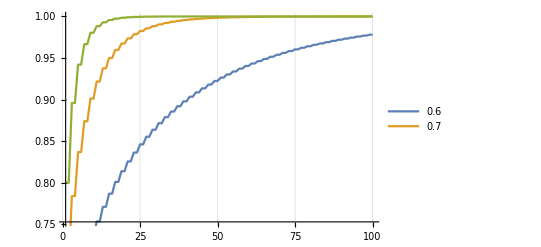

```mathematica
DiscretePlot[{Condorcet[x,0.6],Condorcet[x,0.7],Condorcet[x,0.8]},
{x,1,100},PlotLegends->{0.6,0.7},Filling->None,Joined->True,
GridLines->{ allocationPerc*100,{}}]
```

```mathematica
accuracies={0.6,0.7,0.8};
errors=1-accuracies
Total[errors]
allocationPerc=errors/Total[errors]
Total[allocationPerc]
allocationPerc*100
```

{0.4,0.3,0.2}

0.9

{0.444444,0.333333,0.222222}

1.

{44.4444,33.3333,22.2222}

```mathematica
GetAllocationPerc[accuracies_]:=((1-accuracies)/Total[1-accuracies])
GetAllocationPerc[accuracies]
```

{0.444444,0.333333,0.222222}

```mathematica
GetAllocationPerc[accuracies][[1]]
```

0.444444

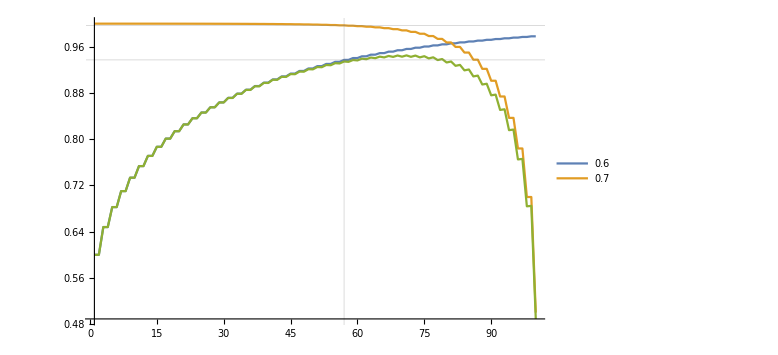

```mathematica
accuracies={0.6,0.7};
agents=100;
DiscretePlot[{Condorcet[x,0.6],Condorcet[agents-x,0.7],
Condorcet[x,0.6]*Condorcet[agents-x,0.7]},
{x,1,agents},PlotLegends->{0.6,0.7},Filling->None,Joined->True,ImageSize->Large,
GridLines->{ {Round[GetAllocationPerc[accuracies][[1]]*agents]},{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],0.6],Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],0.7]}}]
```

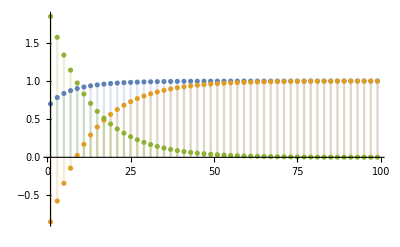

```mathematica
Approximation[n_,p_]:=0.5+Binomial[n,Ceiling[n/2]](Ceiling[n/2]+1)/(4^Ceiling[n/2])(p-0.5)
Approximation1[n_,p_]:=0.5+Sqrt[(2n+1)/Pi](1+1/(16n^2))(p-0.5)
UpperBound[n_,p_]:=2Exp[-2n (p-0.5)^2]
LowerBound[n_,p_]:=1-2Exp[-2n (p-0.5)^2]
DiscretePlot[{Condorcet[x,0.7],LowerBound[x,0.7],UpperBound[x,0.7]},{x,1,100,2}]
```

```mathematica
Expand[Binomial[n,k]]
```

Binomial[n,k]

```mathematica
cc=(n+1)(n+2)-(n+1-k)(n+2-k)
dd=(n-k+1)(n-k+2)
Simplify[cc]
Simplify[Expand[dd]]
Simplify[cc/dd]
Simplify[n!cc/(k!(n-k)!(n-k+1)(n-k+2))]
```

(1+n) (2+n)-(1-k+n) (2-k+n)

(1-k+n) (2-k+n)

k (3-k+2 n)

2+k^2+3 n+n^2-k (3+2 n)

(k (3-k+2 n))/((-2+k-n) (-1+k-n))

-(k (-3+k-2 n) n!)/((-2+k-n) (-1+k-n) k! (-k+n)!)

```mathematica
D[x^2Log[x-1],x]
```

x^2/(-1+x)+2 x Log[-1+x]

(1-p)^(-k+n) p^k Binomial[n,k] (Log[1-p]+PolyGamma[0,1+n]-PolyGamma[0,1-k+n])

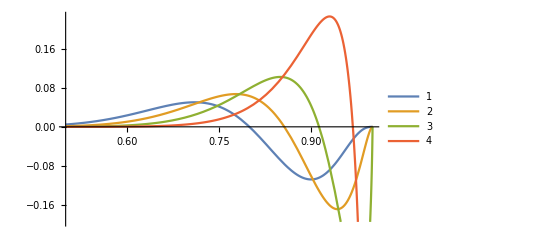

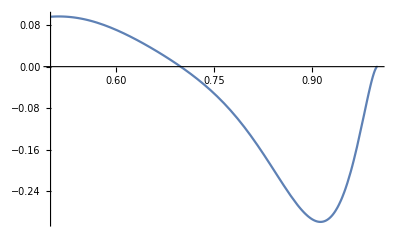

```mathematica
der=Simplify[D[Binomial[n,k]p^k(1-p)^(n-k),n]]
Plot[{der/.{n->17,k->14},
der/.{n->17,k->15},
der/.{n->17,k->16},
der/.{n->17,k->17}},{p,0.5,1},PlotLegends->Automatic]
Plot[(der/.{n->17,k->9})+(der/.{n->17,k->10})+(der/.{n->17,k->11})+(der/.{n->17,k->12})+(der/.{n->17,k->13})+(der/.{n->17,k->14})+(der/.{n->17,k->15}),{p,0.5,1},PlotLegends->Automatic]
```

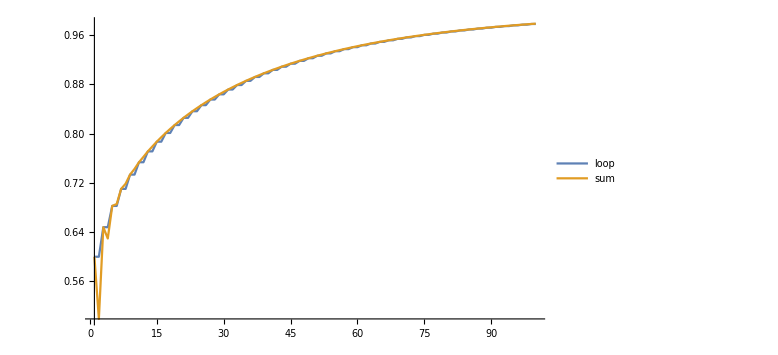

```mathematica
Condorcet2[n_,p_]:=Sum[Binomial[n,k]p^k(1-p)^(n-k),{k,(n+1)/2,n}]
DiscretePlot[{Condorcet[x,0.6],Condorcet2[x,0.6]},{x,1,agents},PlotLegends->{"loop","sum"},Filling->None,Joined->True,ImageSize->Large]
```

```mathematica
der=D[Condorcet2[n,p],n]
```

1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Log[1-p]+1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Log[p]+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] (Binomial[n,(1+n)/2] (PolyGamma[0,1+n]-PolyGamma[0,1+1/2 (-1-n)+n])+1/2 Binomial[n,(1+n)/2] (PolyGamma[0,1+1/2 (-1-n)+n]-PolyGamma[0,1+(1+n)/2]))+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) Binomial[n,(1+n)/2] (1/2 Hypergeometric2F1^(0,0,1,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)]-1/2 Hypergeometric2F1^(0,1,0,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)])

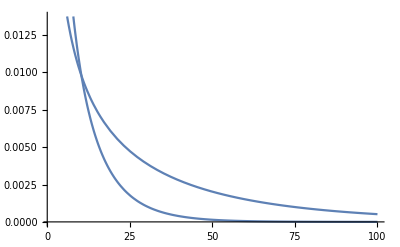

```mathematica
Plot[Table[der/.{p->x},{x,{0.6,0.7}}],{n,1,agents}]
```

```mathematica
Simplify[D[Sum[Binomial[n,k]p^k(1-p)^(n-k),{k,(n+1)/2,n}],n]]
```

1/2 (1-p)^(1/2 (-1+n)) p^((1+n)/2) Binomial[n,(1+n)/2] (Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] (Log[1-p]+Log[p]-PolyGamma[0,(1+n)/2]+2 PolyGamma[0,1+n]-PolyGamma[0,(3+n)/2])+Hypergeometric2F1^(0,0,1,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)]-Hypergeometric2F1^(0,1,0,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)])

```mathematica
der=D[Condorcet2[n,p]*Condorcet2[agents-n,q],n]
```

1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] Log[1-p]+1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] Log[p]-1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] Log[1-q]-1/2 (1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] Log[q]+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] (-Binomial[100-n,(101-n)/2] (PolyGamma[0,101-n]-PolyGamma[0,101+1/2 (-101+n)-n])-1/2 Binomial[100-n,(101-n)/2] (-PolyGamma[0,1+(101-n)/2]+PolyGamma[0,101+1/2 (-101+n)-n]))+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] (Binomial[n,(1+n)/2] (PolyGamma[0,1+n]-PolyGamma[0,1+1/2 (-1-n)+n])+1/2 Binomial[n,(1+n)/2] (PolyGamma[0,1+1/2 (-1-n)+n]-PolyGamma[0,1+(1+n)/2]))+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,1/2 (-99+n),(103-n)/2,q/(-1+q)] (1/2 Hypergeometric2F1^(0,0,1,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)]-1/2 Hypergeometric2F1^(0,1,0,0)[1,(1-n)/2,(3+n)/2,p/(-1+p)])+(1-p)^(1/2 (-1-n)+n) p^((1+n)/2) (1-q)^(100+1/2 (-101+n)-n) q^((101-n)/2) Binomial[100-n,(101-n)/2] Binomial[n,(1+n)/2] Hypergeometric2F1[1,(1-n)/2,(3+n)/2,p/(-1+p)] (-1/2 Hypergeometric2F1^(0,0,1,0)[1,1/2 (-99+n),(103-n)/2,q/(-1+q)]+1/2 Hypergeometric2F1^(0,1,0,0)[1,1/2 (-99+n),(103-n)/2,q/(-1+q)])

```mathematica
Reduce[der==0,{n}]
```

$Aborted

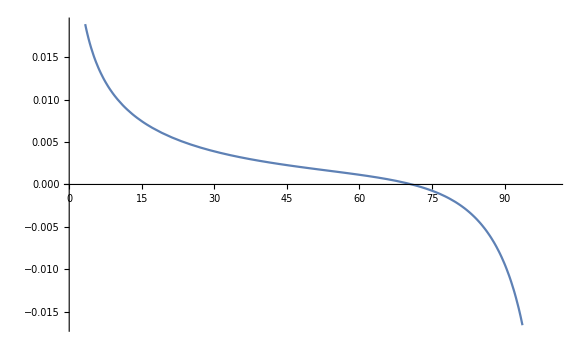

```mathematica
Plot[der/.{p->0.6,q->0.7},{n,1,agents}]
```

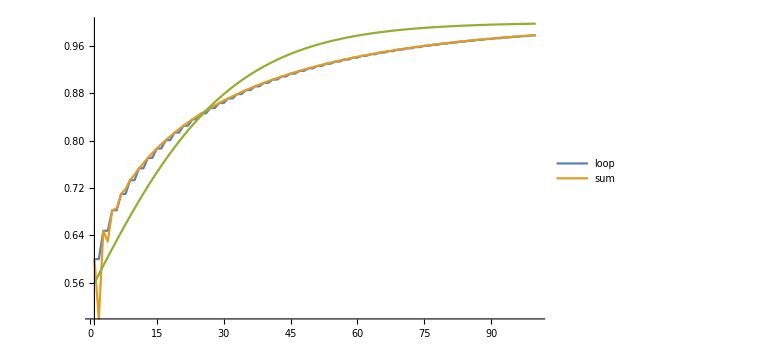

```mathematica
Clear[Approximation]
Approximation[n_,p_,g_]:=1/(1+Exp[-g p(n+3)])
DiscretePlot[{Condorcet[x,0.6],Condorcet2[x,0.6],Approximation[x,0.6,0.1]},{x,1,agents},
PlotLegends->{"loop","sum"},Filling->None,Joined->True,ImageSize->Large]
```

{g→0.0336102,k→100.807}

1/(1+ⅇ^(-0.0336102 p (100.807+x)))

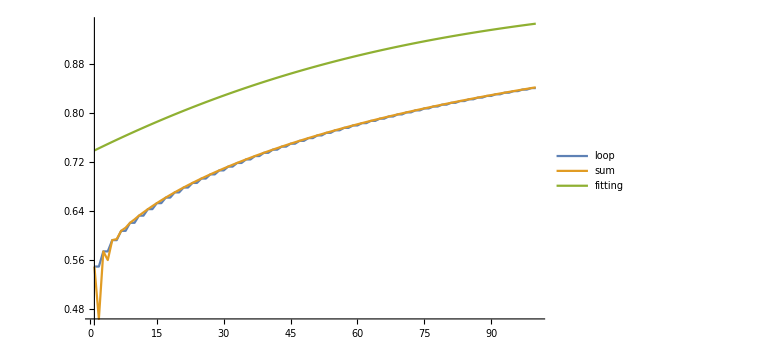

```mathematica
acc=0.55;
data=Catenate[Table[{n,p,Condorcet2[n,p]},{n,Range[1,100,2]},{p,Range[0.55,0.95,0.05]}]];
(*fitted=Fit[data,{1,n,n^-1,n^2,n^3},n]*)
fitted2=FindFit[data,1/(1+Exp[-g p(n+k p)]),{g,k},{n,p}]
1/(1+Exp[-g p(n+k)])/.fitted2/.{n->x}
(*Plot[1/(1+Exp[-g p(n+k)])/.{p->0.7}/.fitted2/.{n->x},{x,1,agents}]*)
DiscretePlot[{Condorcet[x,acc],Condorcet2[x,acc],1/(1+Exp[-g p(n+k p)])/.{p->acc}/.fitted2/.{n->x}},{x,1,agents},
PlotLegends->{"loop","sum","fitting"},Filling->None,Joined->True,ImageSize->Large]
```

```mathematica
Clear[ApproximationLF]
```

```mathematica
ApproximationLF[n_,p_]:=(1/(1+Exp[-g p(n+k p)])/.fitted2)
ApproximationLF[x,acc]
```

1/(1+ⅇ^(-0.0184856 (55.444+x)))

```mathematica
Manipulate[
Plot[ApproximationLF[x,p],{x,1,agents}],{{p,0.6},0.5,1}]
```

```mathematica
Manipulate[
DiscretePlot[{Condorcet[x,p],Condorcet2[x,p],ApproximationLF[x,p]},{x,1,agents},
PlotLegends->{"loop","sum","fitting"},Filling->None,Joined->True,ImageSize->Large]
,{{p,0.6},0.5,1}]
```

{{0.55,0.0141738,28.3953},{0.6,0.0391603,15.7968},{0.65,0.0855598,8.14974},{0.7,0.151029,5.2255},{0.75,0.235255,3.86842},{0.8,0.340902,3.12406},{0.85,0.475893,2.65795},{0.9,0.663101,2.31534},{0.95,0.98464,1.99044}}

{a→1.33934,b→6.10192,c→-0.0120223}

-0.0120223+1.33934 p^6.10192

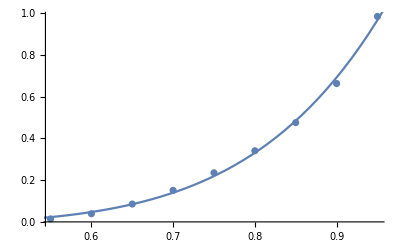

{a→0.22172,b→-8.02635,c→1.67724}

1.67724+0.22172/p^8.02635

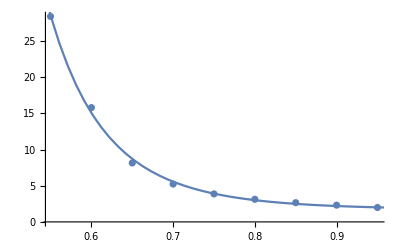

1/(1+ⅇ^(-(1.67724+0.22172/p^8.02635) (-0.0120223+n+1.33934 p^6.10192)))

```mathematica
acc=0.55;
data=Catenate[Table[{n,p,Condorcet2[n,p]},{n,Range[1,100,2]},{p,Range[0.55,0.95,0.05]}]];
(*fitted=Fit[data,{1,n,n^-1,n^2,n^3},n]*)
funcBase[n_]:=1/(1+Exp[-g(n+k)]);
fits=Table[
Join[{p},FindFit[Table[{n,Condorcet2[n,p]},{n,Range[1,100,2]}],funcBase[n],{g,k},n][[All,2]]],
{p,Range[0.55,0.95,0.05]}
]
(*fitG=Fit[fits[[All,{1,2}]],{1,x,x^2},x]*)
funcG[x_]:=a x^b+c
fittingK=FindFit[fits[[All,{1,2}]],funcG[x],{a,b,c},x]
funcK[p]/.fittingK
Show[
ListPlot[fits[[All,{1,2}]]],
(*Plot[{fitG,funcG[x]/.fitting},{x,0.5,1}],*)
Plot[funcK[x]/.fittingK,{x,0.5,1}]
]
(*fitK=Fit[fits[[All,{1,3}]],{1,Exp[x]},x]*)
funcK[x_]:=a x^b+c
fittingG=FindFit[fits[[All,{1,3}]],funcK[x],{a,b,c},x]
funcG[p]/.fittingG
Show[
ListPlot[fits[[All,{1,3}]]],
(*Plot[fitK,{x,0.5,1}],*)
Plot[funcK[x]/.fittingG,{x,0.5,1}]
]
funcApprox[n_,p_]:=funcBase[n]/.{g->funcG[p]/.fittingG,k->funcK[p]/.fittingK}
funcApprox[n,p]
```

```mathematica
Manipulate[
DiscretePlot[{Condorcet[x,p],Condorcet2[x,p],funcApprox[x,p]},{x,1,agents},
PlotLegends->{"loop","sum","fitting"},Filling->None,Joined->True,ImageSize->Large]
,{{p,0.6},0.5,1}]
```

```mathematica
funcX[n_,p_]:=1/(1+ⅇ^(-(a+b/p^c) (0.5+n+f p^c)))
data=Catenate[Table[{n,p,Condorcet2[n,p]},{n,Range[1,100,2]},{p,Range[0.55,0.95,0.05]}]];
fitted2=FindFit[data,funcX[n,p],{a,b,c,f},{n,p}]
funcX[n,p]/.fitted2/.{n->x}
Manipulate[
DiscretePlot[{Condorcet[x,p],Condorcet2[x,p],funcX[x,p]/.fitted2/.{n->x}},{x,1,agents},
PlotLegends->{"loop","sum","fitting"},Filling->None,Joined->True,ImageSize->Large]
,{{p,0.6},0.5,1}]
```

{a→-0.0168114,b→1.83712,c→-6.8205,f→0.458913}

1/(1+ⅇ^((0.0168114-1.83712 p^6.8205) (0.5+0.458913/p^6.8205+x)))

ReplaceAll::reps: {fitted2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {fitted2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
funcX[n,0.6]+funcX[agents-n,0.7]/.fitted2
FindMaximum[funcX[n,0.6]+funcX[agents-n,0.7]/.fitted2,{n,agents/50}]
```

1/(1+ⅇ^(-0.144486 (105.727-n)))+1/(1+ⅇ^(-0.0395545 (15.4572+n)))

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.96193,{n→72.3988}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.962175,{n→72.5222}}

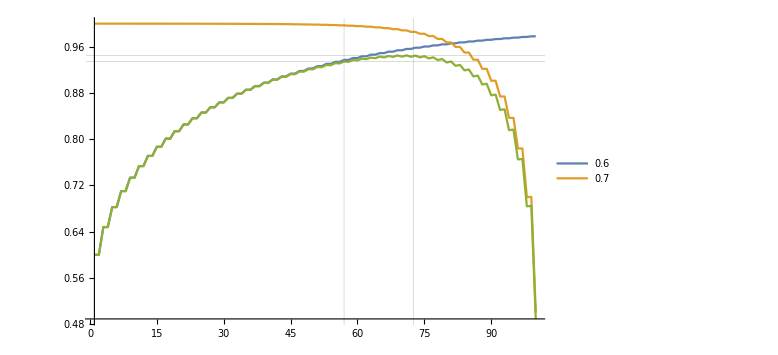

```mathematica
accuracies={0.6,0.7};
agents=100;
mx=FindMaximum[funcX[n,accuracies[[1]]]*funcX[agents-n,accuracies[[2]]]/.fitted2,{n,agents/50}]
DiscretePlot[{Condorcet[x,accuracies[[1]]],Condorcet[agents-x,accuracies[[2]]],
Condorcet[x,accuracies[[1]]]*Condorcet[agents-x,accuracies[[2]]]},
{x,1,agents},PlotLegends->accuracies,Filling->None,Joined->True,ImageSize->Large,
GridLines->{ {Round[GetAllocationPerc[accuracies][[1]]*agents],mx[[2]][[1,2]]},
{(*Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]],Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]],*)
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[agents-Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[2]]],
Condorcet[Round[mx[[2]][[1,2]]],accuracies[[1]]]*Condorcet[agents-Round[mx[[2]][[1,2]]],accuracies[[2]]]}}]
```

-(ⅇ^((0.5+n+0.458913/p^6.8205) (0.0168114-1.83712 p^6.8205)) (-12.5301 (0.5+n+0.458913/p^6.8205) p^5.8205-(3.13001 (0.0168114-1.83712 p^6.8205))/p^7.8205))/((1+ⅇ^((0.5+n+0.458913/p^6.8205) (0.0168114-1.83712 p^6.8205)))^2)

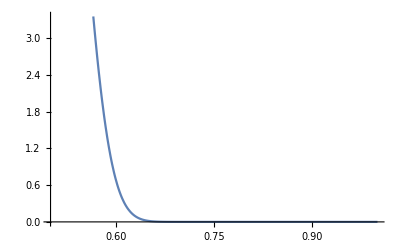

-(ⅇ^((0.5+n+0.458913/p^6.8205) (0.0168114-1.83712 p^6.8205)) (0.0168114-1.83712 p^6.8205))/((1+ⅇ^((0.5+n+0.458913/p^6.8205) (0.0168114-1.83712 p^6.8205)))^2)

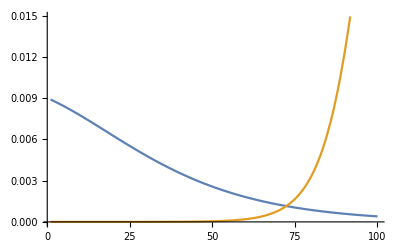

{{m→72.3988}}

```mathematica
derP=D[funcX[n,p]/.fitted2,p]
Plot[derP/.{n->100},{p,0.5,1}]

derN=D[funcX[n,p]/.fitted2,n]
Plot[{derN/.{n->m,p->0.6},derN/.{n->agents-m,p->0.7}},{m,1,agents}]
NSolve[(derN/.{n->m,p->0.6})==(derN/.{n->agents-m,p->0.7})&&m>0&&m<100,m]
```

```mathematica
Plot3D[{derN/.{n->m,p->0.6},derN/.{n->h,p->0.7},derN/.{n->agents-h-m,p->0.8}},{m,1,agents},{h,1,agents}]
NSolve[(derN/.{n->m,p->0.6})==(derN/.{n->h,p->0.7})&&(derN/.{n->h,p->0.7})==(derN/.{n->agents-m-h,p->0.8})&&m>0&&m<100&&m+h<100&&h>0&&h<100,{m,h}]
```

-Graphics3D-

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

NSolve[(0.0395545 ⅇ^(-0.0395545 (15.4572+m)))/((1+ⅇ^(-0.0395545 (15.4572+m)))^2)==(0.144486 ⅇ^(-0.144486 (5.72684+h)))/((1+ⅇ^(-0.144486 (5.72684+h)))^2)&&(0.144486 ⅇ^(-0.144486 (5.72684+h)))/((1+ⅇ^(-0.144486 (5.72684+h)))^2)==(0.384204 ⅇ^(-0.384204 (102.602-h-m)))/((1+ⅇ^(-0.384204 (102.602-h-m)))^2)&&m>0&&m<100&&h+m<100&&h>0&&h<100,{m,h}]

```mathematica
accuracies={0.6,0.7};
agents=100;
mx=FindMaximum[funcX[n,accuracies[[1]]]*funcX[agents-n,accuracies[[2]]]/.fitted2,{n,agents/50}]
DiscretePlot[{Condorcet[x,accuracies[[1]]],Condorcet[agents-x,accuracies[[2]]],
Condorcet[x,accuracies[[1]]]*Condorcet[agents-x,accuracies[[2]]]},
{x,1,agents},PlotLegends->accuracies,Filling->None,Joined->True,ImageSize->Large,
GridLines->{ {Round[GetAllocationPerc[accuracies][[1]]*agents],mx[[2]][[1,2]]},
{(*Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]],Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]],*)
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[agents-Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[2]]],
Condorcet[Round[mx[[2]][[1,2]]],accuracies[[1]]]*Condorcet[agents-Round[mx[[2]][[1,2]]],accuracies[[2]]]}}]
```

{0.942486,{n→63.4141,h→25.0498}}

25

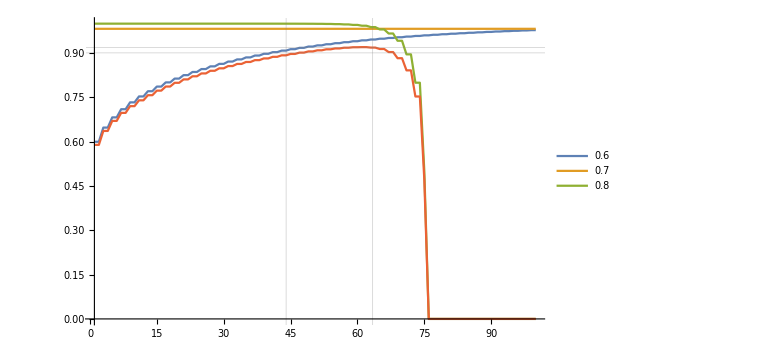

```mathematica
accuracies={0.6,0.7,0.8};
agents=100;
mx=FindMaximum[funcX[n,accuracies[[1]]]*funcX[h,accuracies[[2]]]*funcX[agents-h-n,accuracies[[3]]]/.fitted2,{n,agents/50},{h,agents/50}]
pop2=Round[mx[[2]][[2,2]]]
DiscretePlot[{Condorcet[x,accuracies[[1]]],Condorcet[pop2,accuracies[[2]]],Condorcet[agents-x-pop2,accuracies[[3]]],
Condorcet[x,accuracies[[1]]]*Condorcet[pop2,accuracies[[2]]]*Condorcet[agents-x-pop2,accuracies[[3]]]},
{x,1,agents},PlotLegends->accuracies,Filling->None,Joined->True,ImageSize->Large,
GridLines->{ {Round[GetAllocationPerc[accuracies][[1]]*agents],mx[[2]][[1,2]]},
{(*Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]],Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]],*)
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[agents-Round[GetAllocationPerc[accuracies][[2]]*agents]-Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[3]]],
Condorcet[Round[mx[[2]][[1,2]]],accuracies[[1]]]*Condorcet[pop2,accuracies[[2]]]*Condorcet[agents-pop2-Round[mx[[2]][[1,2]]],accuracies[[3]]]}}]
```

{0.942486,{n→63.4141,h→25.0498}}

{0.922129,{n→60.2973,h→26.2557}}

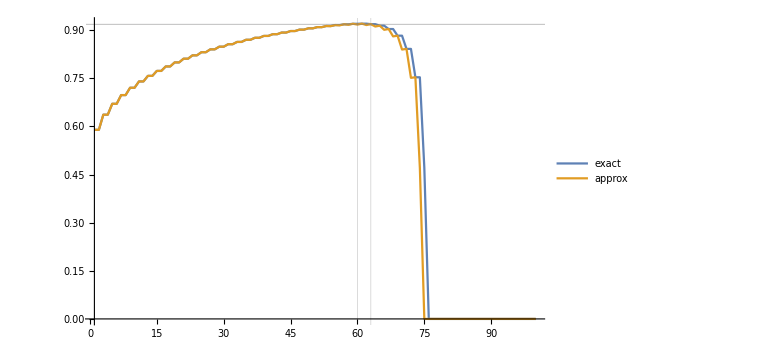

```mathematica
mx1=FindMaximum[funcX[n,accuracies[[1]]]*funcX[h,accuracies[[2]]]*funcX[agents-h-n,accuracies[[3]]]/.fitted2,{n,agents/50},{h,agents/50}]
mx2=FindMaximum[Condorcet2[n,accuracies[[1]]]*Condorcet2[h,accuracies[[2]]]*Condorcet2[agents-h-n,accuracies[[3]]],{n,agents/50},{h,agents/50},AccuracyGoal->3]
DiscretePlot[{
Condorcet[x,accuracies[[1]]]*Condorcet[Round[mx1[[2]][[2,2]]],accuracies[[2]]]*Condorcet[agents-x-Round[mx1[[2]][[2,2]]],accuracies[[3]]],
Condorcet[x,accuracies[[1]]]*Condorcet[Round[mx2[[2]][[2,2]]],accuracies[[2]]]*Condorcet[agents-x-Round[mx2[[2]][[2,2]]],accuracies[[3]]]},
{x,1,agents},PlotLegends->{"exact","approx"},Filling->None,Joined->True,ImageSize->Large,
GridLines->{ {Round[mx1[[2]][[1,2]]],Round[mx2[[2]][[1,2]]]},
{Condorcet[Round[mx1[[2]][[1,2]]],accuracies[[1]]]*Condorcet[Round[mx1[[2]][[2,2]]],accuracies[[2]]]*Condorcet[agents-Round[mx1[[2]][[2,2]]]-Round[mx1[[2]][[1,2]]],accuracies[[3]]],
Condorcet[Round[mx2[[2]][[1,2]]],accuracies[[1]]]*Condorcet[Round[mx2[[2]][[2,2]]],accuracies[[2]]]*Condorcet[agents-Round[mx2[[2]][[2,2]]]-Round[mx2[[2]][[1,2]]],accuracies[[3]]]}}]
```

```mathematica
DiscretePlot3D[{Condorcet[x,accuracies[[1]]],Condorcet[y,accuracies[[2]]],Condorcet[agents-x-y,accuracies[[3]]]},
{x,1,agents},{y,1,agents},Filling->None]
DiscretePlot3D[Condorcet[x,accuracies[[1]]]*Condorcet[y,accuracies[[2]]]*Condorcet[agents-x-y,accuracies[[3]]],{x,1,agents},{y,1,agents}]
```

-Graphics3D-

-Graphics3D-

```mathematica
accuracies={0.6,0.7};
agents=100;
mx1=FindMaximum[Condorcet2[n,accuracies[[1]]]*Condorcet2[agents-n,accuracies[[2]]],{n,agents/50}]
{mx1[[2]][[1,2]],agents-mx1[[2]][[1,2]]}
mx2=0;Do[tmp=Condorcet[n,accuracies[[1]]]*Condorcet[agents-n,accuracies[[2]]];If[tmp>mx2,mx2=tmp;pop2=n;];,{n,Range[1,agents]}];{mx2,pop2}
GetAllocationPerc[accuracies_]:=((1-accuracies)/Total[(1-accuracies)])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;1]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^2/Total[(1-accuracies)^2])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;1]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^3/Total[(1-accuracies)^3])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;1]]]}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.945085,{n→70.8355}}

{70.8355,29.1645}

{0.945083,71}

{0.934498,0.571429,0.428571,57,43}

{0.940235,0.64,0.36,64,36}

{0.942833,0.703297,0.296703,70,30}

```mathematica
accuracies={0.6,0.7,0.9};
agents=100;
mx1=FindMaximum[Condorcet2[n,accuracies[[1]]]*Condorcet2[h,accuracies[[2]]]*Condorcet2[agents-h-n,accuracies[[3]]],{n,agents/50},{h,agents/50}]
{mx1[[2]][[1,2]],mx1[[2]][[2,2]],agents-mx1[[2]][[2,2]]-mx1[[2]][[1,2]]}
mx2=0;pop1=0;pop2=0;
Do[Do[
tmp=Condorcet[n,accuracies[[1]]]*Condorcet[h,accuracies[[2]]]*Condorcet[agents-h-n,accuracies[[3]]];
If[tmp>mx2,mx2=tmp;pop1=n;pop2=h;];,{n,Range[1,agents]}],{h,Range[1,agents]}];
{mx2,pop1,pop2,agents-pop1-pop2}
GetAllocationPerc[accuracies_]:=((1-accuracies)/Total[(1-accuracies)])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]],accuracies[[3]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^2/Total[(1-accuracies)^2])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]],accuracies[[3]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^3/Total[(1-accuracies)^3])
Join[{Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]],accuracies[[3]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;2]]]}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.934242,{n→65.1785,h→27.614}}

{65.1785,27.614,7.20745}

{0.932919,65,27,8}

{0.917289,0.5,0.375,0.125,50,38,12}

{0.911159,0.615385,0.346154,0.0384615,62,35,3}

{0.848549,0.695652,0.293478,0.0108696,70,29,1}

```mathematica
accuracies={0.6,0.7,0.8,0.55};
agents=100;
mx1=FindMaximum[Condorcet2[n,accuracies[[1]]]*Condorcet2[h,accuracies[[2]]]*Condorcet2[g,accuracies[[3]]]*Condorcet2[agents-h-g-n,accuracies[[4]]],{n,agents/50},{h,agents/50},{g,agents/50}]
{mx1[[2]][[1,2]],mx1[[2]][[2,2]],mx1[[2]][[3,2]],agents-mx1[[2]][[2,2]]-mx1[[2]][[1,2]]-mx1[[2]][[3,2]]}
(*mx2=0;
Do[Do[Do[
tmp=Condorcet[n,accuracies[[1]]]*Condorcet[h,accuracies[[2]]]*Condorcet[g,accuracies[[3]]]*Condorcet[agents-h-n-g,accuracies[[4]]];
If[tmp>mx2,mx2=tmp;pop1=n;pop2=h;pop3=g;];,{n,Range[1,agents]}],{h,Range[1,agents]}],{g,Range[1,agents]}];*)
{mx2,pop1,pop2,pop3,agents-pop1-pop2-pop3}
GetAllocationPerc[accuracies_]:=((1-accuracies)/Total[(1-accuracies)])
Join[{
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[Round[GetAllocationPerc[accuracies][[3]]*agents],accuracies[[3]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]],accuracies[[4]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],Round[GetAllocationPerc[accuracies][[3]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^2/Total[(1-accuracies)^2])
Join[{
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[Round[GetAllocationPerc[accuracies][[3]]*agents],accuracies[[3]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]],accuracies[[4]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],Round[GetAllocationPerc[accuracies][[3]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]]}]
GetAllocationPerc[accuracies_]:=((1-accuracies)^3/Total[(1-accuracies)^3])
Join[{
Condorcet[Round[GetAllocationPerc[accuracies][[1]]*agents],accuracies[[1]]]*Condorcet[Round[GetAllocationPerc[accuracies][[2]]*agents],accuracies[[2]]]*Condorcet[Round[GetAllocationPerc[accuracies][[3]]*agents],accuracies[[3]]]*Condorcet[agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]],accuracies[[4]]]},GetAllocationPerc[accuracies],{Round[GetAllocationPerc[accuracies][[1]]*agents],Round[GetAllocationPerc[accuracies][[2]]*agents],Round[GetAllocationPerc[accuracies][[3]]*agents],agents-Total[Round[GetAllocationPerc[accuracies]*agents][[1;;3]]]}]
Condorcet[33,accuracies[[1]]]*Condorcet[18,accuracies[[2]]]*Condorcet[8,accuracies[[3]]]*Condorcet[41,accuracies[[4]]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.614132,{n→34.7003,h→18.5608,g→10.2184}}

{34.7003,18.5608,10.2184,36.5204}

{0.932919,65,27,11,-3}

{0.602225,0.296296,0.222222,0.148148,0.333333,30,22,15,33}

{0.599035,0.324873,0.182741,0.0812183,0.411168,32,18,8,42}

{0.557624,0.336621,0.142012,0.0420776,0.47929,34,14,4,48}

0.60404

```mathematica
num=100;
p1=0.7;
p2=0.6;
ratio=(p1*(1-p1))/(p2*(1-p2))
ratio=Sqrt[(p1*(1-p1))]/Sqrt[(p2*(1-p2))]
v1=Log[p1]/Log[1-p1]
v2=Log[p2]/Log[1-p2]
v1/(v1+v2)
(*ratio=(p2*(1-p2))/(p1*(1-p1))*)
(*ratio=p2/p1*)
Manipulate[
Plot[
{Condorcet2[k*num,p1]*Condorcet2[(1-k)*num,p2]},{k,0.05,0.95},
Frame->True,
Axes->False,
GridLines->{{ratio},{}},
FrameLabel->{"pop1","accuracy"},
ImageSize->500],
{{num,100},10,300}
]
```

0.875

0.935414

0.296248

0.557493

0.347

```mathematica
Reduce[Condorcet2[k*num,p1]==Condorcet2[(1-k)*num,p2]&&k>0&&k<1,k]
```

$Aborted

```mathematica
step=0.05;
allval={};
num=100;
Do[
Do[
val=0;
Do[
tmp=Abs[Condorcet2[k,pf]*Condorcet2[num-k,ps]];
If[tmp>val,
val=tmp;
opt=k;
];
,{k,Range[3,num]}
];
allval=Append[allval,{pf,ps,opt}];
,{pf,Range[0.5+step,1.0-step,step]}
]
,{ps,Range[0.5+step,1.0-step,step]}
]
allval
```

```mathematica
num=100;
allval={{0.55,0.55,50},{0.6000000000000001,0.55,45},{0.65,0.55,33},{0.7000000000000001,0.55,25},{0.75,0.55,17},{0.8,0.55,13},{0.8500000000000001,0.55,9},{0.9000000000000001,0.55,7},{0.95,0.55,5},{0.55,0.6000000000000001,55},{0.6000000000000001,0.6000000000000001,50},{0.65,0.6000000000000001,39},{0.7000000000000001,0.6000000000000001,29},{0.75,0.6000000000000001,21},{0.8,0.6000000000000001,17},{0.8500000000000001,0.6000000000000001,11},{0.9000000000000001,0.6000000000000001,9},{0.95,0.6000000000000001,5},{0.55,0.65,67},{0.6000000000000001,0.65,61},{0.65,0.65,50},{0.7000000000000001,0.65,39},{0.75,0.65,29},{0.8,0.65,23},{0.8500000000000001,0.65,17},{0.9000000000000001,0.65,11},{0.95,0.65,7},{0.55,0.7000000000000001,75},{0.6000000000000001,0.7000000000000001,71},{0.65,0.7000000000000001,61},{0.7000000000000001,0.7000000000000001,50},{0.75,0.7000000000000001,39},{0.8,0.7000000000000001,31},{0.8500000000000001,0.7000000000000001,23},{0.9000000000000001,0.7000000000000001,17},{0.95,0.7000000000000001,11},{0.55,0.75,83},{0.6000000000000001,0.75,79},{0.65,0.75,71},{0.7000000000000001,0.75,61},{0.75,0.75,50},{0.8,0.75,41},{0.8500000000000001,0.75,31},{0.9000000000000001,0.75,23},{0.95,0.75,17},{0.55,0.8,87},{0.6000000000000001,0.8,83},{0.65,0.8,77},{0.7000000000000001,0.8,69},{0.75,0.8,59},{0.8,0.8,49},{0.8500000000000001,0.8,41},{0.9000000000000001,0.8,31},{0.95,0.8,23},{0.55,0.8500000000000001,91},{0.6000000000000001,0.8500000000000001,89},{0.65,0.8500000000000001,83},{0.7000000000000001,0.8500000000000001,77},{0.75,0.8500000000000001,69},{0.8,0.8500000000000001,59},{0.8500000000000001,0.8500000000000001,49},{0.9000000000000001,0.8500000000000001,41},{0.95,0.8500000000000001,29},{0.55,0.9000000000000001,93},{0.6000000000000001,0.9000000000000001,91},{0.65,0.9000000000000001,89},{0.7000000000000001,0.9000000000000001,83},{0.75,0.9000000000000001,77},{0.8,0.9000000000000001,69},{0.8500000000000001,0.9000000000000001,59},{0.9000000000000001,0.9000000000000001,49},{0.95,0.9000000000000001,35},{0.55,0.95,95},{0.6000000000000001,0.95,95},{0.65,0.95,93},{0.7000000000000001,0.95,89},{0.75,0.95,83},{0.8,0.95,77},{0.8500000000000001,0.95,71},{0.9000000000000001,0.95,57},{0.95,0.95,35}};
```

```mathematica
err[p_]:=p*(1-p)
(*err[p_]:=Sqrt[p*(1-p)]
err[p_]:=Log[p]/Log[1-p]
err[p_]:=(1-p)/p*)
Show[
ListPlot3D[allval,ImageSize->Large],
Plot3D[err[pf]/(err[pf]+err[ps])*num,{pf,step,1-step},{ps,step,1-step},ColorFunction->"Rainbow"]
]
```

-Graphics3D-

```mathematica
step=0.05;
allval={};
Do[
Do[
val=0;
Do[
tmp=Abs[Condorcet2[k,pf]*Condorcet2[num-k,0.6]];
If[tmp>val,
val=tmp;
opt=k/num;
];
,{k,Range[3,num]}
];
allval=Append[allval,{pf,num,opt}];
,{pf,Range[0.5+step,1.0-step,step]}
]
,{num,Range[10,500,10]}
]
allval
```

```mathematica
allval={{0.55,10,3/10},{0.6000000000000001,10,1/2},{0.65,10,1/2},{0.7000000000000001,10,1/2},{0.75,10,1/2},{0.8,10,1/2},{0.8500000000000001,10,3/10},{0.9000000000000001,10,3/10},{0.95,10,3/10},{0.55,20,7/20},{0.6000000000000001,20,9/20},{0.65,20,11/20},{0.7000000000000001,20,9/20},{0.75,20,7/20},{0.8,20,7/20},{0.8500000000000001,20,1/4},{0.9000000000000001,20,1/4},{0.95,20,3/20},{0.55,30,13/30},{0.6000000000000001,30,1/2},{0.65,30,1/2},{0.7000000000000001,30,13/30},{0.75,30,11/30},{0.8,30,3/10},{0.8500000000000001,30,7/30},{0.9000000000000001,30,1/6},{0.95,30,1/10},{0.55,40,9/20},{0.6000000000000001,40,1/2},{0.65,40,9/20},{0.7000000000000001,40,3/8},{0.75,40,13/40},{0.8,40,9/40},{0.8500000000000001,40,7/40},{0.9000000000000001,40,1/8},{0.95,40,3/40},{0.55,50,12/25},{0.6000000000000001,50,1/2},{0.65,50,11/25},{0.7000000000000001,50,17/50},{0.75,50,3/10},{0.8,50,11/50},{0.8500000000000001,50,9/50},{0.9000000000000001,50,7/50},{0.95,50,1/10},{0.55,60,1/2},{0.6000000000000001,60,1/2},{0.65,60,5/12},{0.7000000000000001,60,7/20},{0.75,60,1/4},{0.8,60,13/60},{0.8500000000000001,60,3/20},{0.9000000000000001,60,7/60},{0.95,60,1/12},{0.55,70,18/35},{0.6000000000000001,70,1/2},{0.65,70,29/70},{0.7000000000000001,70,23/70},{0.75,70,17/70},{0.8,70,13/70},{0.8500000000000001,70,9/70},{0.9000000000000001,70,1/10},{0.95,70,1/14},{0.55,80,21/40},{0.6000000000000001,80,1/2},{0.65,80,2/5},{0.7000000000000001,80,5/16},{0.75,80,19/80},{0.8,80,3/16},{0.8500000000000001,80,11/80},{0.9000000000000001,80,7/80},{0.95,80,1/16},{0.55,90,49/90},{0.6000000000000001,90,1/2},{0.65,90,2/5},{0.7000000000000001,90,3/10},{0.75,90,7/30},{0.8,90,1/6},{0.8500000000000001,90,11/90},{0.9000000000000001,90,1/10},{0.95,90,1/18},{0.55,100,11/20},{0.6000000000000001,100,1/2},{0.65,100,39/100},{0.7000000000000001,100,29/100},{0.75,100,21/100},{0.8,100,17/100},{0.8500000000000001,100,11/100},{0.9000000000000001,100,9/100},{0.95,100,1/20},{0.55,110,31/55},{0.6000000000000001,110,1/2},{0.65,110,21/55},{0.7000000000000001,110,31/110},{0.75,110,23/110},{0.8,110,17/110},{0.8500000000000001,110,13/110},{0.9000000000000001,110,9/110},{0.95,110,7/110},{0.55,120,23/40},{0.6000000000000001,120,1/2},{0.65,120,23/60},{0.7000000000000001,120,11/40},{0.75,120,5/24},{0.8,120,19/120},{0.8500000000000001,120,13/120},{0.9000000000000001,120,3/40},{0.95,120,7/120},{0.55,130,38/65},{0.6000000000000001,130,1/2},{0.65,130,49/130},{0.7000000000000001,130,7/26},{0.75,130,5/26},{0.8,130,19/130},{0.8500000000000001,130,1/10},{0.9000000000000001,130,9/130},{0.95,130,7/130},{0.55,140,83/140},{0.6000000000000001,140,1/2},{0.65,140,13/35},{0.7000000000000001,140,37/140},{0.75,140,27/140},{0.8,140,19/140},{0.8500000000000001,140,3/28},{0.9000000000000001,140,11/140},{0.95,140,1/20},{0.55,150,3/5},{0.6000000000000001,150,1/2},{0.65,150,11/30},{0.7000000000000001,150,4/15},{0.75,150,29/150},{0.8,150,7/50},{0.8500000000000001,150,1/10},{0.9000000000000001,150,11/150},{0.95,150,7/150},{0.55,160,97/160},{0.6000000000000001,160,1/2},{0.65,160,29/80},{0.7000000000000001,160,21/80},{0.75,160,29/160},{0.8,160,21/160},{0.8500000000000001,160,3/32},{0.9000000000000001,160,11/160},{0.95,160,7/160},{0.55,170,52/85},{0.6000000000000001,170,1/2},{0.65,170,61/170},{0.7000000000000001,170,22/85},{0.75,170,31/170},{0.8,170,23/170},{0.8500000000000001,170,1/10},{0.9000000000000001,170,11/170},{0.95,170,7/170},{0.55,180,28/45},{0.6000000000000001,180,1/2},{0.65,180,13/36},{0.7000000000000001,180,23/90},{0.75,180,11/60},{0.8,180,23/180},{0.8500000000000001,180,17/180},{0.9000000000000001,180,11/180},{0.95,180,7/180},{0.55,190,119/190},{0.6000000000000001,190,1/2},{0.65,190,34/95},{0.7000000000000001,190,47/190},{0.75,190,33/190},{0.8,190,5/38},{0.8500000000000001,190,17/190},{0.9000000000000001,190,13/190},{0.95,190,9/190},{0.55,200,63/100},{0.6000000000000001,200,1/2},{0.65,200,71/200},{0.7000000000000001,200,49/200},{0.75,200,7/40},{0.8,200,1/8},{0.8500000000000001,200,19/200},{0.9000000000000001,200,13/200},{0.95,200,9/200},{0.55,210,67/105},{0.6000000000000001,210,1/2},{0.65,210,37/105},{0.7000000000000001,210,17/70},{0.75,210,37/210},{0.8,210,9/70},{0.8500000000000001,210,19/210},{0.9000000000000001,210,13/210},{0.95,210,3/70},{0.55,220,141/220},{0.6000000000000001,220,1/2},{0.65,220,7/20},{0.7000000000000001,220,53/220},{0.75,220,37/220},{0.8,220,27/220},{0.8500000000000001,220,19/220},{0.9000000000000001,220,13/220},{0.95,220,9/220},{0.55,230,149/230},{0.6000000000000001,230,1/2},{0.65,230,8/23},{0.7000000000000001,230,11/46},{0.75,230,39/230},{0.8,230,27/230},{0.8500000000000001,230,19/230},{0.9000000000000001,230,13/230},{0.95,230,9/230},{0.55,240,13/20},{0.6000000000000001,240,1/2},{0.65,240,83/240},{0.7000000000000001,240,19/80},{0.75,240,1/6},{0.8,240,29/240},{0.8500000000000001,240,7/80},{0.9000000000000001,240,1/16},{0.95,240,3/80},{0.55,250,82/125},{0.6000000000000001,250,1/2},{0.65,250,43/125},{0.7000000000000001,250,59/250},{0.75,250,41/250},{0.8,250,29/250},{0.8500000000000001,250,21/250},{0.9000000000000001,250,3/50},{0.95,250,9/250},{0.55,260,171/260},{0.6000000000000001,260,1/2},{0.65,260,89/260},{0.7000000000000001,260,61/260},{0.75,260,43/260},{0.8,260,31/260},{0.8500000000000001,260,21/260},{0.9000000000000001,260,3/52},{0.95,260,9/260},{0.55,270,179/270},{0.6000000000000001,270,1/2},{0.65,270,46/135},{0.7000000000000001,270,7/30},{0.75,270,22/135},{0.8,270,31/270},{0.8500000000000001,270,23/270},{0.9000000000000001,270,1/18},{0.95,270,11/270},{0.55,280,93/140},{0.6000000000000001,280,1/2},{0.65,280,19/56},{0.7000000000000001,280,13/56},{0.75,280,9/56},{0.8,280,33/280},{0.8500000000000001,280,23/280},{0.9000000000000001,280,3/56},{0.95,280,11/280},{0.55,290,97/145},{0.6000000000000001,290,1/2},{0.65,290,49/145},{0.7000000000000001,290,67/290},{0.75,290,47/290},{0.8,290,33/290},{0.8500000000000001,290,23/290},{0.9000000000000001,290,17/290},{0.95,290,11/290},{0.55,300,101/150},{0.6000000000000001,300,1/2},{0.65,300,17/50},{0.7000000000000001,300,23/100},{0.75,300,4/25},{0.8,300,11/100},{0.8500000000000001,300,1/12},{0.9000000000000001,300,17/300},{0.95,300,11/300},{0.55,310,209/310},{0.6000000000000001,310,1/2},{0.65,310,21/62},{0.7000000000000001,310,71/310},{0.75,310,49/310},{0.8,310,7/62},{0.8500000000000001,310,5/62},{0.9000000000000001,310,17/310},{0.95,310,11/310},{0.55,320,217/320},{0.6000000000000001,320,1/2},{0.65,320,27/80},{0.7000000000000001,320,73/320},{0.75,320,5/32},{0.8,320,7/64},{0.8500000000000001,320,5/64},{0.9000000000000001,320,17/320},{0.95,320,11/320},{0.55,330,15/22},{0.6000000000000001,330,1/2},{0.65,330,37/110},{0.7000000000000001,330,5/22},{0.75,330,26/165},{0.8,330,37/330},{0.8500000000000001,330,5/66},{0.9000000000000001,330,17/330},{0.95,330,1/30},{0.55,340,58/85},{0.6000000000000001,340,1/2},{0.65,340,57/170},{0.7000000000000001,340,77/340},{0.75,340,53/340},{0.8,340,37/340},{0.8500000000000001,340,27/340},{0.9000000000000001,340,19/340},{0.95,340,11/340},{0.55,350,24/35},{0.6000000000000001,350,1/2},{0.65,350,117/350},{0.7000000000000001,350,79/350},{0.75,350,27/175},{0.8,350,39/350},{0.8500000000000001,350,27/350},{0.9000000000000001,350,19/350},{0.95,350,13/350},{0.55,360,31/45},{0.6000000000000001,360,1/2},{0.65,360,1/3},{0.7000000000000001,360,2/9},{0.75,360,11/72},{0.8,360,13/120},{0.8500000000000001,360,3/40},{0.9000000000000001,360,19/360},{0.95,360,13/360},{0.55,370,128/185},{0.6000000000000001,370,1/2},{0.65,370,123/370},{0.7000000000000001,370,41/185},{0.75,370,57/370},{0.8,370,39/370},{0.8500000000000001,370,29/370},{0.9000000000000001,370,19/370},{0.95,370,13/370},{0.55,380,263/380},{0.6000000000000001,380,1/2},{0.65,380,63/190},{0.7000000000000001,380,21/95},{0.75,380,29/190},{0.8,380,41/380},{0.8500000000000001,380,29/380},{0.9000000000000001,380,1/20},{0.95,380,13/380},{0.55,390,271/390},{0.6000000000000001,390,1/2},{0.65,390,43/130},{0.7000000000000001,390,43/195},{0.75,390,59/390},{0.8,390,41/390},{0.8500000000000001,390,29/390},{0.9000000000000001,390,7/130},{0.95,390,1/30},{0.55,400,279/400},{0.6000000000000001,400,1/2},{0.65,400,33/100},{0.7000000000000001,400,11/50},{0.75,400,61/400},{0.8,400,43/400},{0.8500000000000001,400,29/400},{0.9000000000000001,400,21/400},{0.95,400,13/400},{0.55,410,7/10},{0.6000000000000001,410,1/2},{0.65,410,27/82},{0.7000000000000001,410,9/41},{0.75,410,31/205},{0.8,410,43/410},{0.8500000000000001,410,31/410},{0.9000000000000001,410,21/410},{0.95,410,13/410},{0.55,420,7/10},{0.6000000000000001,420,1/2},{0.65,420,23/70},{0.7000000000000001,420,23/105},{0.75,420,3/20},{0.8,420,3/28},{0.8500000000000001,420,31/420},{0.9000000000000001,420,1/20},{0.95,420,13/420},{0.55,430,151/215},{0.6000000000000001,430,1/2},{0.65,430,141/430},{0.7000000000000001,430,47/215},{0.75,430,32/215},{0.8,430,9/86},{0.8500000000000001,430,31/430},{0.9000000000000001,430,21/430},{0.95,430,3/86},{0.55,440,31/44},{0.6000000000000001,440,1/2},{0.65,440,18/55},{0.7000000000000001,440,12/55},{0.75,440,3/20},{0.8,440,9/88},{0.8500000000000001,440,3/40},{0.9000000000000001,440,23/440},{0.95,440,3/88},{0.55,450,53/75},{0.6000000000000001,450,1/2},{0.65,450,49/150},{0.7000000000000001,450,49/225},{0.75,450,67/450},{0.8,450,47/450},{0.8500000000000001,450,11/150},{0.9000000000000001,450,23/450},{0.95,450,1/30},{0.55,460,163/230},{0.6000000000000001,460,1/2},{0.65,460,15/46},{0.7000000000000001,460,5/23},{0.75,460,17/115},{0.8,460,47/460},{0.8500000000000001,460,33/460},{0.9000000000000001,460,1/20},{0.95,460,3/92},{0.55,470,333/470},{0.6000000000000001,470,1/2},{0.65,470,153/470},{0.7000000000000001,470,51/235},{0.75,470,69/470},{0.8,470,49/470},{0.8500000000000001,470,33/470},{0.9000000000000001,470,23/470},{0.95,470,3/94},{0.55,480,341/480},{0.6000000000000001,480,1/2},{0.65,480,13/40},{0.7000000000000001,480,103/480},{0.75,480,71/480},{0.8,480,49/480},{0.8500000000000001,480,7/96},{0.9000000000000001,480,23/480},{0.95,480,1/32},{0.55,490,349/490},{0.6000000000000001,490,1/2},{0.65,490,159/490},{0.7000000000000001,490,3/14},{0.75,490,36/245},{0.8,490,51/490},{0.8500000000000001,490,1/14},{0.9000000000000001,490,5/98},{0.95,490,3/98},{0.55,500,357/500},{0.6000000000000001,500,1/2},{0.65,500,81/250},{0.7000000000000001,500,107/500},{0.75,500,73/500},{0.8,500,51/500},{0.8500000000000001,500,7/100},{0.9000000000000001,500,1/20},{0.95,500,3/100}};
```

```mathematica
ListPlot3D[allval,ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[allval,ImageSize->Large],
Plot3D[err[pf]/(err[pf]+err[0.6]),{pf,step,1-step},{num,10,500},ColorFunction->"Rainbow"]
]
```

-Graphics3D-